```mathematica
载流圆线圈的磁力线分布——折线法
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in φ near {φ} = {1.68115}. NIntegrate obtained -1.40946×10^-18 and 5.40265×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in φ near {φ} = {4.70002}. NIntegrate obtained 3.17129×10^-18 and 8.22821×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in φ near {φ} = {1.49707}. NIntegrate obtained 8.13152×10^-18 and 1.07352×10^-17 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

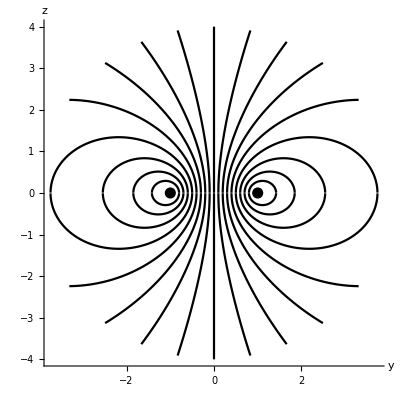

```mathematica
By[y_,z_]:=
NIntegrate[(R*z*Sin[φ])/((y^2+z^2+R^2-2y*R*Sin[φ])^(3/2)),
{φ,0,2π}];
Bz[y_,z_]:=
NIntegrate[(R*(R-y*Sin[φ]))/((y^2+z^2+R^2-2y*R*Sin[φ])^(3/2)),
{φ,0,2π}];
R=1.0;r1=step=0.005 R;r2=4 R;forceline={};
Do[
θ=π/2.0;p={y0,r1};single={p};
While[(Abs[p[[2]]]>=r1)∧(Norm[p]<r2),
AppendTo[single,p];
p=p+step*{Cos[θ],Sin[θ]};
θ=Arg[By[p[[1]],p[[2]]]
+ⅈ*Bz[p[[1]],p[[2]]]]];
AppendTo[forceline,single];m=Length[single];single=Table[{single[[j,1]],-single[[j,2]]},
{j,m}];AppendTo[forceline,single],
{y0,-8R/10,8R/10,R/10}]
Show[
Graphics[{Thickness[0.004],Line/@forceline}],
Axes->True,AxesLabel->{"y","z"},
AxesStyle->Thickness[0.003],AspectRatio->1,
Epilog->{PointSize[0.02],
Point/@{{-R,0},{R,0}}}]
Clear[By,Bz]
```